## Rural

```mathematica
f[x_]:=0.25 + 0.05*If[x<10,x,
If[x<30, 0.5*x+5,
If[x<60, x/3+10,
If[x<100,x/4+15,
If[x<150,x/5+20,
If[x<210,x/6+25,
If[x<280,x/7+30,
If[x<360,x/8+35,
If[x<450,x/9+40,
If[x<550,x/10+45, 
If[x<660,x/11+50, 
If[x<780,x/12+55, 
If[x<910,x/13+60, 
If[x<1050,x/14+65, 
If[x<1200,x/15+70, 150]
]
]
]
]
]
]
]
]
]
]
]
]
]
]
```

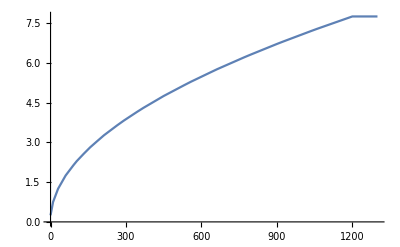

```mathematica
Plot[f[x],{x,0,1300}]
```

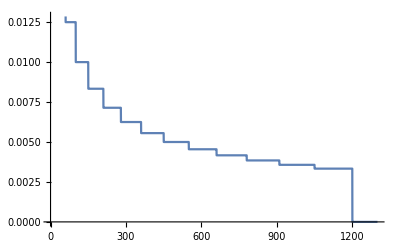

```mathematica
Plot[D[f[y],y]/.y->x,{x,0,1300}]
```

```mathematica
w[currentpop_, currentinfra_, extrainfra_,decay_] := 0.5(currentpop+extrainfra*0.001)  f[(currentinfra+extrainfra)/(currentpop+extrainfra*0.001)]/f[(currentinfra)/(currentpop)] currentSurplus-(currentinfra+extrainfra)*decay
```

```mathematica
ReturnOnInvestmentTime[currentpop_, currentinfra_, decay_]:=1/(D[w[currentpop, currentinfra, extrainfra,decay],extrainfra])/.extrainfra->0
```

```mathematica
FullSimplify[ReturnOnInvestmentTime[pop, infra,decay]]
```

Piecewise[{{2000./(1. currentSurplus-2000. decay), infra/pop≥1200}, {(-1. infra-5. pop)/(1. decay infra-0.5025 currentSurplus pop+5. decay pop), infra pop<10 pop^2}, {(-1. infra-20. pop)/(1. decay infra-0.51 currentSurplus pop+20. decay pop), infra/pop<30&&infra pop≥10 pop^2}, {(-1. infra-45. pop)/(1. decay infra-0.5225 currentSurplus pop+45. decay pop), 30≤infra/pop<60}, {(-1. infra-80. pop)/(1. decay infra-0.54 currentSurplus pop+80. decay pop), 60≤infra/pop<100}, {(-1. infra-125. pop)/(1. decay infra-0.5625 currentSurplus pop+125. decay pop), 100≤infra/pop<150}, {(-1. infra-180. pop)/(1. decay infra-0.59 currentSurplus pop+180. decay pop), 150≤infra/pop<210}, {(-1. infra-245. pop)/(1. decay infra-0.6225 currentSurplus pop+245. decay pop), 210≤infra/pop<280}, {(-1. infra-320. pop)/(1. decay infra-0.66 currentSurplus pop+320. decay pop), 280≤infra/pop<360}, {(-1. infra-405. pop)/(1. decay infra-0.7025 currentSurplus pop+405. decay pop), 360≤infra/pop<450}, {(-1. infra-500. pop)/(1. decay infra-0.75 currentSurplus pop+500. decay pop), 450≤infra/pop<550}, {(-1. infra-605. pop)/(1. decay infra-0.8025 currentSurplus pop+605. decay pop), 550≤infra/pop<660}, {(-1. infra-720. pop)/(1. decay infra-0.86 currentSurplus pop+720. decay pop), 660≤infra/pop<780}, {(-1. infra-845. pop)/(1. decay infra-0.9225 currentSurplus pop+845. decay pop), 780≤infra/pop<910}, {(-1. infra-980. pop)/(1. decay infra-0.99 currentSurplus pop+980. decay pop), 910≤infra/pop<1050}, {(-1. infra-1125. pop)/(1. decay infra-1.0625 currentSurplus pop+1125. decay pop), True}}]

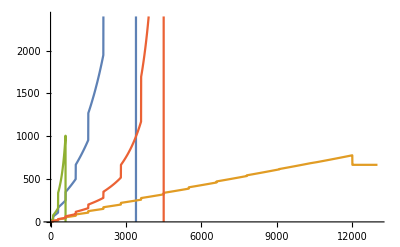

```mathematica
Plot[{
ReturnOnInvestmentTime[10, infra,0.001]/.currentSurplus->1,
ReturnOnInvestmentTime[10, infra,0.001]/.currentSurplus->5,
ReturnOnInvestmentTime[10, infra,0.004]/.currentSurplus->1,
ReturnOnInvestmentTime[10, infra,0.004]/.currentSurplus->5
},{infra, 0,13000},PlotRange->{0,2400}]
```

## Cities

```mathematica
q[x_]:= (x/50)/(x/500+0.2)
```

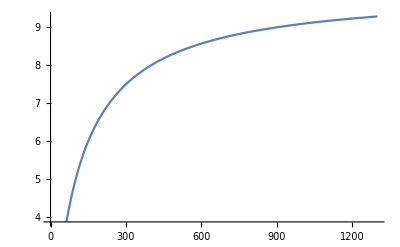

```mathematica
Plot[{q[x]},{x,0,1300}]
```

```mathematica
w[currentpop_, currentinfra_, extrainfra_,decay_] := 0.25(currentpop+extrainfra*0.001)  q[(currentinfra+extrainfra)/(currentpop+extrainfra*0.001)]-(currentinfra+extrainfra)*decay
```

```mathematica
ReturnOnInvestmentTime[currentpop_, currentinfra_, decay_]:=1/(D[w[currentpop, currentinfra, extrainfra,decay],extrainfra])/.extrainfra->0
```

```mathematica
FullSimplify[ReturnOnInvestmentTime[pop, infra,decay]]
```

-(1. (0.+infra+100. pop)^2)/((-0.0025+decay) infra^2+(4.44089×10^-16+200. decay) infra pop+(-250.+10000. decay) pop^2)

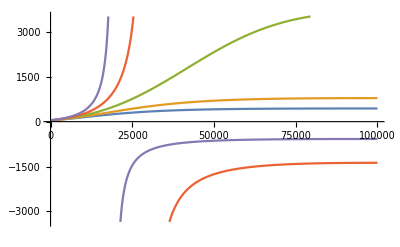

```mathematica
Plot[{
ReturnOnInvestmentTime[100, infra,0.000],
ReturnOnInvestmentTime[100, infra,0.001],
ReturnOnInvestmentTime[100, infra,0.002],
ReturnOnInvestmentTime[100, infra,0.003],
ReturnOnInvestmentTime[100, infra,0.004]
},{infra, 0,100000}]
```